```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/qtc325/Trabalhos/NBIA/2024_09_QNMResonantExcitation_ElephantFlea/SphericalSym_ElephFlea_TimeEvol/ExternalCodes

## Parameters

## Physical Parameters

### Wave equation Parameters

```mathematica
Mbh=rh/2;
λ=rh;
spin=2;
l=2;
```

### Bump Parameters

```mathematica
ModelName="BumpPT";
 ao=10; (*120000/10000;*)(*115722/10000;*)
 ϵ=0(*204/100000;*)
```

0

## Numerical Parameters

```mathematica
Prec=10*MachinePrecision;

Nz$dom0=75;
Nz$dom1=75;

NzRef$dom0=70;
NzRef$dom1=70;
ϵQNM=10^(-4); (*Relative error between QNMs from different resolutions*)
```

## Schwarzschild Spacetime

## Metric Function

```mathematica
a=1-rh/r;
b=a;
f=FullSimplify[Sqrt[a*b], Assumptions->{rh>0, r>rh}];
ζ$of$r=FullSimplify[Sqrt[a/b], Assumptions->{rh>0, r>rh}];
```

```mathematica
m=r/2*(1-b);

fAsymp=Normal@Series[f,{r,Infinity,1}]//Expand;
M$ADM=-Coefficient[fAsymp,r,-1]/2//FullSimplify;
SubsM={M->M$ADM}
```

{M→rh/2}

## Hyperboloidal Formulation

## Radial Compactfication

### Areal Radius

```mathematica
ρ1=0;(*rh/λ 1/(1-σ0)*)
ρ0=rh/λ-ρ1;

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify;
```

### Radial Mapping

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ;
dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]];
```

```mathematica
σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]];
```

### Metric function and deviation function in compact coordinate

```mathematica
F=Simplify[f/.r->r$of$σ[σ]];
ζ=Simplify[ζ$of$r/.r->r$of$σ[σ]];
```

#### Find Horizons

```mathematica
SubsσHrz=Solve[{F==0, σ>0},σ,Reals];
σHrz=σ/.SubsσHrz;
nHrz=Length@σHrz;
rHrz=r$of$σ[σHrz];
```

#### Representation as in eq. 2.13 - Event Horizon

```mathematica
root$rh=(1-rHrz/r)/.r->r$of$σ[σ]//FullSimplify;
Kh=Expand[F/root$rh]//FullSimplify;
```

## Dimensionless Tortoise Coordinate

### Differential Equation (eq. 2.11)

```mathematica
dx$dσ=FullSimplify[-β/(σ^2F)];
```

### Contribution from Infinity (eq. 4.7)

```mathematica
x$0=ρ0/σ-2M/λ Log[σ];
dx0$dσ=FullSimplify[D[x$0,σ]];
```

### Contribution from Event Horizon (eq. 4.5)

```mathematica
KBHHrz=Table[Limit[Kh[[i]],SubsσHrz[[i]]],{i,1,nHrz}];
x$BHHrz=Table[rHrz[[i]]/(λ*KBHHrz[[i]])*Log[σHrz[[i]]-σ],{i,1,nHrz}];

dx$BHHrz$dσ=Table[D[x$BHHrz[[i]],σ],{i,1,nHrz}];
```

### Regular Contribution

```mathematica
dx$dσ$Reg=dx$dσ-dx0$dσ - Sum[dx$BHHrz$dσ[[i]],{i,1,nHrz}]/.SubsM;
Subs$dxdσ$Reg=x$Reg'[σ]->dx$dσ$Reg;
```

#### Check Tortoise

```mathematica
x$Reg[σ_]:=0;
x=x$0+ Sum[x$BHHrz[[i]],{i,1,nHrz}]+x$Reg[σ]/.SubsM//Simplify;
dx$dσ$Paper=D[x,σ]/.Subs$dxdσ$Reg;
FullSimplify[dx$dσ$Paper==dx$dσ]
```

True

## Height Function

### Out-In Strategy

```mathematica
H=-x$0 +Sum[x$BHHrz[[i]],{i,1,nHrz}]-x$Reg[σ]/.SubsM//Simplify;
dH$dσ=D[H,σ]/.Subs$dxdσ$Reg;
```

### Metric Functions

```mathematica
p=FullSimplify[-1/dx$dσ]
(*Plot[p/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

-((-1+σ) σ^2)

```mathematica
γ=dH$dσ*p//FullSimplify
(*Plot[γ/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

1-2 σ^2

```mathematica
(*Series[γ,{σ,σHrz[[1]],0}]*)
w=(1-γ^2)/p//FullSimplify
(*Plot[w/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->{0,All}]*)
```

4 (1+σ)

## Wave Equation

## Regge Wheeler Potential

```mathematica
If[spin==0,VRW=a/r^2*(l*(l+1) + r*D[a*b,r]/(2*a))];
If[Abs@spin==2, VRW=a/r^2* ( l*(l+1) - 6m/r + D[m,r])];

qRW=λ^2/p * VRW/.r->r$of$σ[σ]//FullSimplify
```

6-3 σ

### Bump

```mathematica
Vbump =  λ^(-2) Sech[x-ao]^2/.r->r$of$σ[σ]//FullSimplify;
(* λ^(-2) Exp[ -(x-ao)^2/(2 δ)  ]*)

qBump=λ^2/p * Vbump;
```

```mathematica
If[ϵ==0,
σBump=1/2,
σBump=σ/.N[Solve[x-ao==0,σ],50*MachinePrecision][[1]]
];
```

### Final Potential

```mathematica
V = VRW + ϵ Vbump/.r->r$of$σ[σ];
q = λ^2/p * V//FullSimplify;
```

## Eigenvalue Solver

## Discrete Functions and Matrices

### AnMR

```mathematica
x$of$χ[χ_,κ_,xb_]:= xb(1- 2 Sinh[ κ (1-xb χ)]/Sinh[2κ]    );
χ$of$x[X_,κ_,xb_]:=xb*(1-ArcSinh[(1 - X*xb)*Sinh[2κ]/2]/κ);
```

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_, κ_, xb_, Prec_]:=Module[
{nc, Nc, χ, y},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);
χ=χ$of$x[y,κ,xb];

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,χ],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
x=.

zi=0;
zp=σBump;
zf=1;

Δz$dom0=zp-zi;
Δz$dom1=zf-zp;


nz$dom0=Nz$dom0+1; (*Total number of points*)
nz$dom1=Nz$dom1+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];

χ$dom0=N[Table[x[i,Nz$dom0],{i,0,Nz$dom0}],Prec];
χ$dom1=N[Table[x[i,Nz$dom1],{i,0,Nz$dom1}],Prec];

ZeroArray$dom0=ConstantArray[0,nz$dom0];
ZeroArray$dom1=ConstantArray[0,nz$dom1];
```

```mathematica
nzRef$dom0=NzRef$dom0+1; (*Total number of points*)

nzRef$dom1=NzRef$dom1+1; (*Total number of points*)



χRef$dom0=N[Table[x[i,NzRef$dom0],{i,0,NzRef$dom0}],Prec];
χRef$dom1=N[Table[x[i,NzRef$dom1],{i,0,NzRef$dom1}],Prec];

ZeroArrayRef$dom0=ConstantArray[0,nzRef$dom0];
ZeroArrayRef$dom1=ConstantArray[0,nzRef$dom1];
```

#### AnMR Parameter

DOMAIN 0 σ ∈ [0, σbump]

```mathematica
xb$dom0=1;

κ$dom0=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

If[κ$dom0==0,
X$dom0=χ$dom0;
XRef$dom0=χRef$dom0,

X$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χ$dom0)]/Sinh[2*κ$dom0]),Prec];
XRef$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χRef$dom0)]/Sinh[2*κ$dom0]),Prec];
];
z$dom0=N[zi+1/2 Δz$dom0*(1+X$dom0),Prec];
zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];
```

DOMAIN 1 σ ∈ [σbump,1]

```mathematica
xb$dom1=-1;
κ$dom1=125/100 * ao^(3/10);
If[κ$dom1==0,
X$dom1=χ$dom1;
XRef$dom1=χRef$dom1
,
X$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χ$dom1)]/Sinh[2*κ$dom1]),Prec];
XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];
];
z$dom1=N[zp+1/2 Δz$dom1*(1+X$dom1),Prec];
zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];
```

### Differentiation Matrices

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

Domain 0

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom0=DiffMatrix[-1,1,Nz$dom0,Prec]; 
D2χ$dom0=Dχ$dom0 . Dχ$dom0;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom0],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom0=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom0=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom0=IdentityMatrix[nz$dom0];
Zero$dom0=ConstantArray[0,{nz$dom0,nz$dom0}];
Zero$dom0dom1=ConstantArray[0,{nz$dom0,nz$dom1}];
```

Loading Differentiation Matrices

```mathematica
fnRef$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[NzRef$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fnRef$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[NzRef$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fnRef$Dχ];
check$D2x=FileExistsQ[fnRef$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
DχRef$dom0=DiffMatrix[-1,1,NzRef$dom0,Prec]; 
D2χRef$dom0=DχRef$dom0 . DχRef$dom0;
Export[fnRef$Dχ,IntegerPart[10^(Prec+10)*DχRef$dom0],"Table"];
Export[fnRef$D2χ,IntegerPart[10^(Prec+10)*D2χRef$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
DχRef$dom0=N[Import[fnRef$Dχ,"Table"]/10^(Prec+10),Prec];
D2χRef$dom0=N[Import[fnRef$D2χ,"Table"]/10^(Prec+10),Prec];
]

IdRef$dom0=IdentityMatrix[nzRef$dom0];
ZeroRef$dom0=ConstantArray[0,{nzRef$dom0,nzRef$dom0}];
ZeroRef$dom0dom1=ConstantArray[0,{nzRef$dom0,nzRef$dom1}];
```

Calculating Differentiation Matrices

Domain 1

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom1=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom1=Dχ$dom1 . Dχ$dom1;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom1],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom1=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom1=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom1=IdentityMatrix[nz$dom1];
Zero$dom1=ConstantArray[0,{nz$dom1,nz$dom1}];
Zero$dom1dom0=ConstantArray[0,{nz$dom1,nz$dom0}];

fnRef$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[NzRef$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fnRef$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[NzRef$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fnRef$Dχ];
check$D2x=FileExistsQ[fnRef$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
DχRef$dom1=DiffMatrix[-1,1,NzRef$dom1,Prec]; 
D2χRef$dom1=DχRef$dom1 . DχRef$dom1;
Export[fnRef$Dχ,IntegerPart[10^(Prec+10)*DχRef$dom1],"Table"];
Export[fnRef$D2χ,IntegerPart[10^(Prec+10)*D2χRef$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
DχRef$dom1=N[Import[fnRef$Dχ,"Table"]/10^(Prec+10),Prec];
D2χRef$dom1=N[Import[fnRef$D2χ,"Table"]/10^(Prec+10),Prec];
]

IdRef$dom1=IdentityMatrix[nzRef$dom1];
ZeroRef$dom1=ConstantArray[0,{nzRef$dom1,nzRef$dom1}];
ZeroRef$dom1dom0=ConstantArray[0,{nzRef$dom1,nzRef$dom0}];
```

Loading Differentiation Matrices

Calculating Differentiation Matrices

#### Map derivatives δχ into δx

Domain 0

```mathematica
If[κ$dom0==0,
Dx$dom0=Dχ$dom0;
D2x$dom0=D2χ$dom0;

DxRef$dom0=DχRef$dom0;
D2xRef$dom0=D2χRef$dom0;

,

J =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2 =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

Dx$dom0 = N[Dχ$dom0/J,Prec];
D2x$dom0 = N[(D2χ$dom0 - J2*Dx$dom0)/J^2,Prec];

JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];
];
```

Domain 1

```mathematica
If[κ$dom1==0,
Dx$dom1=Dχ$dom1;
D2x$dom1=D2χ$dom1;

DxRef$dom1=DχRef$dom1;
D2xRef$dom1=D2χRef$dom1
,

J =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2 =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

Dx$dom1 = N[Dχ$dom1/J,Prec];
D2x$dom1 = N[(D2χ$dom1 - J2*Dx$dom1)/J^2,Prec];

JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];
];
```

#### Re-scale Derivative Operators

```mathematica
Dσ$dom0=2/Δz$dom0 * Dx$dom0;
D2σ$dom0=(2/Δz$dom0)^2 * D2x$dom0;

DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;
```

```mathematica
Dσ$dom1=2/Δz$dom1 * Dx$dom1;
D2σ$dom1=(2/Δz$dom1)^2 * D2x$dom1;

DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;
```

#### TEST OPERATORS

(SET TO NON-EVALUATED: CHANGE IF NEED TO TEST)

```mathematica
(*fTest[σ_]:=Cos[2*π*σ]*Exp[-σ^2]*)
(*fVec$dom0=fTest[z$dom0];*)
(*fVec$dom1=fTest[z$dom1];*)
(**)
(*Error$dσ$dom0=Total[Dσ$dom0 . fVec$dom0-fTest'[z$dom0]]*)
(*Error$dσ$dom1=Total[Dσ$dom1 . fVec$dom1-fTest'[z$dom1]]*)
(**)
(**)
(*Error$dσdσ$dom0=Total[Dσ$dom0 . Dσ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$dσdσ$dom1=Total[Dσ$dom1 . Dσ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
(**)
(**)
(*Error$d2σ$dom0=Total[D2σ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$d2σ$dom1=Total[D2σ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
```

### Discrete Functions

```mathematica
p$dom0=p/.σ->z$dom0;
p$dom1=p/.σ->z$dom1;

dp$dom0=D[p,σ]/.σ->z$dom0;
dp$dom1=D[p,σ]/.σ->z$dom1;

γ$dom0=γ/.σ->z$dom0;
γ$dom1=γ/.σ->z$dom1;

dγ$dom0=D[γ,σ]/.σ->z$dom0;
dγ$dom1=D[γ,σ]/.σ->z$dom1;

w$dom0=w/.σ->z$dom0;
w$dom1=w/.σ->z$dom1;

q$dom0=Limit[q,σ->z$dom0, Direction->"FromAbove"];
q$dom1=Limit[q,σ->z$dom1, Direction->"FromBelow"];
```

```mathematica
pRef$dom0=p/.σ->zRef$dom0;
pRef$dom1=p/.σ->zRef$dom1;

dpRef$dom0=D[p,σ]/.σ->zRef$dom0;
dpRef$dom1=D[p,σ]/.σ->zRef$dom1;

γRef$dom0=γ/.σ->zRef$dom0;
γRef$dom1=γ/.σ->zRef$dom1;

dγRef$dom0=D[γ,σ]/.σ->zRef$dom0;
dγRef$dom1=D[γ,σ]/.σ->zRef$dom1;

wRef$dom0=w/.σ->zRef$dom0;
wRef$dom1=w/.σ->zRef$dom1;

qRef$dom0=Limit[q,σ->zRef$dom0, Direction->"FromAbove"];
qRef$dom1=Limit[q,σ->zRef$dom1, Direction->"FromBelow"];

(*cq$dom0=ChebLobattoCoefficients[q$dom0,Prec];
cq$dom1=ChebLobattoCoefficients[q$dom1,Prec];
ListLogPlot[{Abs@cq$dom0,Abs@cq$dom1},PlotLabel->"Cheb Coeff func Pot", PlotStyle->{Red,Purple}]*)
```

```mathematica
(*Plot$p=Plot[p,{σ,0,1}];
Plot$pVec$dom0=ListPlot[Transpose@{z$dom0,p$dom0}, PlotStyle->Red];
Plot$pVec$dom1=ListPlot[Transpose@{z$dom1,p$dom1}, PlotStyle->Purple];
Show[Plot$p,Plot$pVec$dom0,Plot$pVec$dom1]

Plot$γ=Plot[γ,{σ,0,1}];
Plot$γVec$dom0=ListPlot[Transpose@{z$dom0,γ$dom0}, PlotStyle->Red];
Plot$γVec$dom1=ListPlot[Transpose@{z$dom1,γ$dom1}, PlotStyle->Purple];
Show[Plot$γ,Plot$γVec$dom0,Plot$γVec$dom1]

Plot$w=Plot[w//Simplify,{σ,0,1}, WorkingPrecision->100];
Plot$wVec$dom0=ListPlot[Transpose@{z$dom0,w$dom0}, PlotStyle->Red];
Plot$wVec$dom1=ListPlot[Transpose@{z$dom1,w$dom1}, PlotStyle->Purple];
Show[Plot$w,Plot$wVec$dom0,Plot$wVec$dom1]

Plot$q=Plot[q//Simplify,{σ,0,1}, WorkingPrecision->100];
Plot$qVec$dom0=ListPlot[Transpose@{z$dom0,q$dom0}, PlotStyle->Red];
Plot$qVec$dom1=ListPlot[Transpose@{z$dom1,q$dom1}, PlotStyle->Purple];
Show[Plot$q,Plot$qVec$dom0,Plot$qVec$dom1]*)
```

#### Chebyshev Coefficients

```mathematica
(*cp$dom0=ChebLobattoCoefficients[p$dom0,Prec];
cp$dom1=ChebLobattoCoefficients[p$dom1,Prec];
ListLogPlot[{Abs@cp$dom0,Abs@cp$dom1}, PlotLabel->"Cheb Coeff func p", PlotStyle->{Red,Purple}]

cγ$dom0=ChebLobattoCoefficients[γ$dom0,Prec];
cγ$dom1=ChebLobattoCoefficients[γ$dom1,Prec];
ListLogPlot[{Abs@cγ$dom0, Abs@cγ$dom1},PlotLabel->"Cheb Coeff func γ", PlotStyle->{Red,Purple}]

cw$dom0=ChebLobattoCoefficients[w$dom0,Prec];
cw$dom1=ChebLobattoCoefficients[w$dom1,Prec];
ListLogPlot[{Abs@cw$dom0,Abs@cw$dom1},PlotLabel->"Cheb Coeff func w", PlotStyle->{Red,Purple}]*)

(*cq$dom0=ChebLobattoCoefficients[q$dom0,Prec];
cq$dom1=ChebLobattoCoefficients[q$dom1,Prec];
ListLogPlot[{Abs@cq$dom0,Abs@cq$dom1},PlotLabel->"Cheb Coeff func Pot", PlotStyle->{Red,Purple}]*)
```

## QNM Eigenvalue Problem

### Discrete ODE operators

```mathematica
L1$dom0=p$dom0*D2σ$dom0 + dp$dom0*Dσ$dom0 - q$dom0*Id$dom0;
L1$dom1=p$dom1*D2σ$dom1 + dp$dom1*Dσ$dom1 - q$dom1*Id$dom1;

L2$dom0=2*γ$dom0*Dσ$dom0 + dγ$dom0*Id$dom0 ;
L2$dom1=2*γ$dom1*Dσ$dom1 + dγ$dom1*Id$dom1 ;

L=N[ArrayFlatten[{
{     Zero$dom0  ,       Id$dom0   ,  Zero$dom0dom1,     Zero$dom0dom1} , 
{  L1$dom0/w$dom0,   L2$dom0/w$dom0,  Zero$dom0dom1,     Zero$dom0dom1} ,
{     Zero$dom1dom0  ,       Zero$dom1dom0   ,  Zero$dom1,     Id$dom1},
{     Zero$dom1dom0  ,       Zero$dom1dom0   ,  L1$dom1/w$dom1,     L2$dom1/w$dom1}
}],
Prec];

B=IdentityMatrix[2 (nz$dom0+nz$dom1)];

L1Ref$dom0=pRef$dom0*D2σRef$dom0 + dpRef$dom0*DσRef$dom0 - qRef$dom0*IdRef$dom0;
L1Ref$dom1=pRef$dom1*D2σRef$dom1 + dpRef$dom1*DσRef$dom1 - qRef$dom1*IdRef$dom1;

L2Ref$dom0=2*γRef$dom0*DσRef$dom0 + dγRef$dom0*IdRef$dom0 ;
L2Ref$dom1=2*γRef$dom1*DσRef$dom1 + dγRef$dom1*IdRef$dom1 ;

LRef=N[ArrayFlatten[{
{     ZeroRef$dom0  ,       IdRef$dom0   ,  ZeroRef$dom0dom1,     ZeroRef$dom0dom1} , 
{  L1Ref$dom0/wRef$dom0,   L2Ref$dom0/wRef$dom0,  ZeroRef$dom0dom1,     ZeroRef$dom0dom1} ,
{     ZeroRef$dom1dom0  ,       ZeroRef$dom1dom0   ,  ZeroRef$dom1,     IdRef$dom1},
{     ZeroRef$dom1dom0  ,       ZeroRef$dom1dom0   ,  L1Ref$dom1/wRef$dom1,     L2Ref$dom1/wRef$dom1}
}],
Prec];

BRef=IdentityMatrix[2 (nzRef$dom0+nzRef$dom1)];
```

#### Continuity of the function at the domain boundary

```mathematica
B[[nz$dom0+1,All]]=0;
L[[nz$dom0+1,All]]=0;
L[[nz$dom0+1,1]]=1;
L[[nz$dom0+1,2*nz$dom0+nz$dom1]]=-1;

BRef[[nzRef$dom0+1,All]]=0;
LRef[[nzRef$dom0+1,All]]=0;
LRef[[nzRef$dom0+1,1]]=1;
LRef[[nzRef$dom0+1,2*nzRef$dom0+nzRef$dom1]]=-1;
```

#### Continuity of the function's Derivative at the domain boundary

```mathematica
B[[2*nz$dom0+nz$dom1+1,All]]=0;
L[[2*nz$dom0+nz$dom1+1,All]]=0;
L[[2*nz$dom0+nz$dom1+1, ;;nz$dom0]]=Dσ$dom0[[1, All]];
L[[2*nz$dom0+nz$dom1+1, 2*nz$dom0+1;;2*nz$dom0+nz$dom1]]=-Dσ$dom1[[-1, All]];

BRef[[2*nzRef$dom0+nzRef$dom1+1,All]]=0;
LRef[[2*nzRef$dom0+nzRef$dom1+1,All]]=0;
LRef[[2*nzRef$dom0+nzRef$dom1+1, ;;nzRef$dom0]]=DσRef$dom0[[1, All]];
LRef[[2*nzRef$dom0+nzRef$dom1+1, 2*nzRef$dom0+1;;2*nzRef$dom0+nzRef$dom1]]=-DσRef$dom1[[-1, All]];
```

### Solve Eigenvalue

```mathematica
Print["\t\tCalculating QNM values and Functions"];
EigenSol=Eigensystem[{L,B}];
Print["\t\tDone"];

Print["\t\tCalculating QNM References"];
EigenSolRef=Eigenvalues[{LRef,BRef}];
Print["\t\tDone"];
```

Calculating QNM values and Functions

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

Done

Calculating QNM References

Done

#### Re-scale Laplace to Fourier

```mathematica
ω=-I*EigenSol[[1]];
u=EigenSol[[2]];

ωRef=-I*EigenSolRef;
```

Part::partd: Part specification EigenSol⟦1⟧ is longer than depth of object.

Part::partd: Part specification EigenSol⟦2⟧ is longer than depth of object.

```mathematica
ϕQNM$dom0=Table[u[[All,i  ]],{i,1,nz$dom0}   ];
ϕQNM$dom1=Table[u[[All,i  ]],{i,2*nz$dom0+1,nz$dom1}   ];
ϕQNM=Join[ϕQNM$dom0,ϕQNM$dom1];
```

#### Filter discrete from continuous spectra

```mathematica
QNM$filter[x_,y_,z_]:=Block[{list={}},tab=y;tab1=z;Do[Do[If[Abs[(tab[[-j]]-tab1[[-i]])/tab[[-j]]]<x
(*If[Abs[(tab[[-j]][[1]]-tab1[[-i]][[1]])/tab[[-j]][[1]]]<x∧Abs[(tab[[-j]][[2]]-tab1[[-i]][[2]])/tab[[-j]][[2]]]<x*),AppendTo[list,tab1[[-i]]]],{j,1,Length[tab]}],{i,1,Length[tab1]}];list]
```

```mathematica
PosQNMLong=Position[EigenSol[[1]],x_/; Im@x!=0 && Re@x < 0]//Flatten;
nQNMLong=Length@PosQNMLong;
ω$QNMLong=Table[ω[[PosQNMLong[[i]]]],{i,1,nQNMLong}];
u$QNMLong=Table[u[[PosQNMLong[[i]]]],{i,1,nQNMLong}];

PosBranch=Position[EigenSol[[1]],x_/;Im@x==0]//Flatten;
nBranch=Length@PosBranch;
ω$BranchCut=Table[ω[[PosBranch[[i]]]],{i,1,nBranch}];

BranchCutData=Table[{Re@ω$BranchCut[[iqnm]],Im@ω$BranchCut[[iqnm]]},{iqnm,1,nBranch}];
```

```mathematica
PosQNMRef=Position[EigenSolRef,x_/; Im@x!=0 && Re@x < 0]//Flatten;
nRefQNM=Length@PosQNMRef;
ωRef$QNM=Table[ωRef[[PosQNMRef[[i]]]],{i,1,nRefQNM}];

ω$QNM=QNM$filter[ϵQNM,ωRef$QNM,ω$QNMLong];
PosQNM=Position[ω$QNMLong, x_ /; MemberQ[ω$QNM, x]] // Flatten//Reverse

nQNM=Length@PosQNM;
QNMData=Table[{Re@ω$QNM[[iqnm]],Im@ω$QNM[[iqnm]]},{iqnm,1,nQNM}];
u$QNM=u$QNMLong[[PosQNM]];

ϕQNM$Norm=Table[u$QNM[[iQNM,2*nz$dom0+1]],{iQNM,1,nQNM}];

ϕQNM$dom0=Table[u$QNM[[iQNM,i]]/ϕQNM$Norm[[iQNM]],{iQNM,1,nQNM},{i,1,nz$dom0}];
ϕQNM$dom1=Table[u$QNM[[iQNM,i]]/ϕQNM$Norm[[iQNM]],{iQNM,1,nQNM},{i,2*nz$dom0+1,2*nz$dom0+nz$dom1}];

ϕQNM$dom0$data=Table[Transpose@{z$dom0,ϕQNM$dom0[[iQNM]]},{iQNM,1,nQNM}];
ϕQNM$dom1$data=Table[Transpose@{z$dom1,ϕQNM$dom1[[iQNM]]},{iQNM,1,nQNM}];
```

{204,203,202,201,200,199,198,197,196,195}

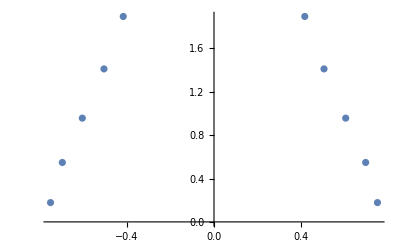

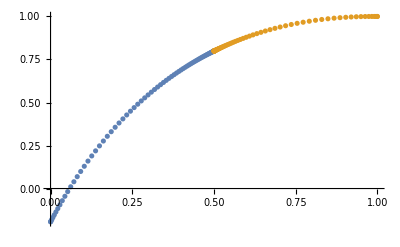

```mathematica
ListPlot[QNMData (*, PlotRange->{{0.7,0.75}, {0,1}}*)]
PlotQNMFunc=ListPlot[{Re@ϕQNM$dom0$data[[1]],Re@ϕQNM$dom1$data[[1]]}, (*Joined->True,*) PlotRange->All]
```

### QNM Data for post-processing

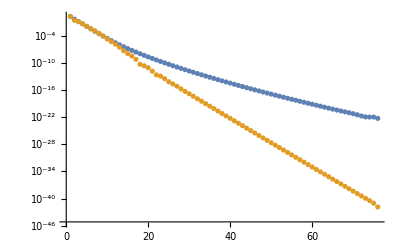

```mathematica
s$n0=I*(QNMData[[All,1]] + I*QNMData[[All,2]]);

cheb$ϕQNM$dom0=Table[ChebLobattoCoefficients[ϕQNM$dom0[[iQNM]],Prec],{iQNM,1,nQNM}];
cheb$ϕQNM$dom1=Table[ChebLobattoCoefficients[ϕQNM$dom1[[iQNM]],Prec],{iQNM,1,nQNM}];

ListLogPlot[{Abs@cheb$ϕQNM$dom0[[1]],Abs@cheb$ϕQNM$dom1[[1]] }]
```

## Export Data

### Initial Data Data C code Pure QNM Evolution

```mathematica
DirName$InputData="../input_data/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm]
If[!DirectoryQ[DirName$InputData],CreateDirectory[DirName$InputData]]

For[iQNM=0, iQNM<nQNM/2, iQNM++,

Nz=Nz$dom0;

fn=DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[iQNM]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat";
NumericalData={
"s\t"<>ToString[Re[s$n0[[2*iQNM+1]]]]<>"\t"<>ToString[Im[s$n0[[2*iQNM+1]]]]<>"\n",
"N\t"<>ToString[Nz]<>"\n\n"
};

fp=OpenWrite[fn];
Table[ WriteString[fp,NumericalData[[i]]], {i,1,Length@NumericalData}];

WriteString[fp,"#1:i\t #2:Real(Cheb_phi_QNM)\t #3:Imag(Cheb_phi_QNM)\n"]
For[i=0, i<=Nz, i++,
WriteString[fp,ToString[i],"\t",
ToString[Re[cheb$ϕQNM$dom0[[2*iQNM+1,i+1]]],CForm],"\t", ToString[Im[cheb$ϕQNM$dom0[[2*iQNM+1,i+1]]],CForm],"\n"]] ;
Close[fp];

Nz=Nz$dom1;
fn=DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[iQNM]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat";
NumericalData={
"s\t"<>ToString[Re[s$n0[[2*iQNM+1]]]]<>"\t"<>ToString[Im[s$n0[[2*iQNM+1]]]]<>"\n",
"N\t"<>ToString[Nz]<>"\n\n"
};

fp=OpenWrite[fn];
Table[ WriteString[fp,NumericalData[[i]]], {i,1,Length@NumericalData}];

WriteString[fp,"#1:i\t #2:Real(Cheb_phi_QNM)\t #3:Imag(Cheb_phi_QNM)\n"]
For[i=0, i<=Nz, i++,
WriteString[fp,ToString[i],"\t",
ToString[Re[cheb$ϕQNM$dom1[[2*iQNM+1,i+1]]],CForm],"\t", ToString[Im[cheb$ϕQNM$dom1[[2*iQNM+1,i+1]]],CForm],"\n"]] 
Close[fp];

]
```

../input_data/eps_0._a0_Over_rh_10.

### Amplitude ExtractionEvolution

```mathematica
DirName$InputData="QNM_Eigenfunctions/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];
If[!DirectoryQ[DirName$InputData],CreateDirectory[DirName$InputData]]

For[iQNM=0, iQNM<nQNM/2, iQNM++,

Nz=Nz$dom0;

fn=DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[iQNM]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat";
NumericalData={
"s\t"<>ToString[Re[s$n0[[2*iQNM+1]]]]<>"\t"<>ToString[Im[s$n0[[2*iQNM+1]]]]<>"\n",
"N\t"<>ToString[Nz]<>"\n\n"
};

fp=OpenWrite[fn];
Table[ WriteString[fp,NumericalData[[i]]], {i,1,Length@NumericalData}];

WriteString[fp,"#1:i\t #2:Real(Cheb_phi_QNM)\t #3:Imag(Cheb_phi_QNM)\n"]
For[i=0, i<=Nz, i++,
WriteString[fp,ToString[i],"\t",
ToString[Re[cheb$ϕQNM$dom0[[2*iQNM+1,i+1]]],CForm],"\t", ToString[Im[cheb$ϕQNM$dom0[[2*iQNM+1,i+1]]],CForm],"\n"]] ;
Close[fp];

Nz=Nz$dom1;
fn=DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[iQNM]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat";;
NumericalData={
"s\t"<>ToString[Re[s$n0[[2*iQNM+1]]]]<>"\t"<>ToString[Im[s$n0[[2*iQNM+1]]]]<>"\n",
"N\t"<>ToString[Nz]<>"\n\n"
};

fp=OpenWrite[fn];
Table[ WriteString[fp,NumericalData[[i]]], {i,1,Length@NumericalData}];

WriteString[fp,"#1:i\t #2:Real(Cheb_phi_QNM)\t #3:Imag(Cheb_phi_QNM)\n"]
For[i=0, i<=Nz, i++,
WriteString[fp,ToString[i],"\t",
ToString[Re[cheb$ϕQNM$dom1[[2*iQNM+1,i+1]]],CForm],"\t", ToString[Im[cheb$ϕQNM$dom1[[2*iQNM+1,i+1]]],CForm],"\n"]] 
Close[fp];

]
```